```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap3D[];
sizes={16,16,16};
timeStep=0.001;
k=0;
contactInteractionFactor=4 Pi k;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{16,16,16} | 3 | 4096 | {5,5,5} | {-5,-5,-5} | {2/3,2/3,2/3} | {(3 π)/16,(3 π)/16,(3 π)/16} | {(3 π)/2,(3 π)/2,(3 π)/2}

time | energies | moments | misc
(0) | (total | 1.5
kinetic | 0.75
potential | 0.75
contact | 0.
virial | -5.3682×10^-8) | (meanX | 0
meanY | 0
meanZ | 0
sigmaX | 0.707107
sigmaY | 0.707107
sigmaZ | 0.707107
norm | 1.) | (steps | 0
A0 | 0.409185)

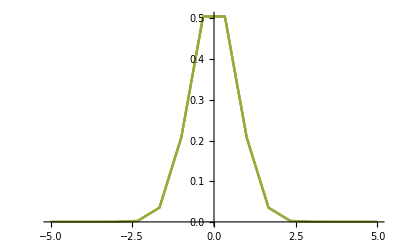

```mathematica
calcAllTable
plotProjections
```

```mathematica
AbsoluteTiming[evolve["ite",2.5,5]]
```

{3.74397,Null}

time | energies | moments | misc
(2.5) | (total | 1.5
kinetic | 0.749628
potential | 0.750373
contact | 0.
virial | -0.00149004) | (meanX | 0
meanY | 0
meanZ | 0
sigmaX | 0.707282
sigmaY | 0.707282
sigmaZ | 0.707282
norm | 1.) | (steps | 2500
A0 | 0.409046)

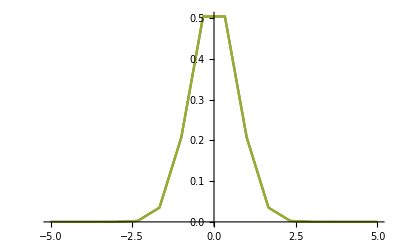

```mathematica
calcAllTable
plotProjections
```

```mathematica
reportEnergies
```

time | total | kinetic | potential | contact | virial
0 | 1.5 | 0.75 | 0.75 | 0. | -5.3682×10^-8
0.5 | 1.5 | 0.749763 | 0.750237 | 0. | -0.000948294
1. | 1.5 | 0.749676 | 0.750324 | 0. | -0.00129713
1.5 | 1.5 | 0.749644 | 0.750356 | 0. | -0.00142546
2. | 1.5 | 0.749632 | 0.750368 | 0. | -0.00147267
2.5 | 1.5 | 0.749628 | 0.750373 | 0. | -0.00149004

```mathematica
reportMoments
```

time | meanX | meanY | meanZ | sigmaX | sigmaY | sigmaZ | norm
0 | 0 | 0 | 0 | 0.707107 | 0.707107 | 0.707107 | 1.
0.5 | 0 | 0 | 0 | 0.707219 | 0.707219 | 0.707219 | 1.
1. | 0 | 0 | 0 | 0.70726 | 0.70726 | 0.70726 | 1.
1.5 | 0 | 0 | 0 | 0.707275 | 0.707275 | 0.707275 | 1.
2. | 0 | 0 | 0 | 0.70728 | 0.70728 | 0.70728 | 1.
2.5 | 0 | 0 | 0 | 0.707282 | 0.707282 | 0.707282 | 1.